```mathematica
c := 3*10^(10) 
G:= 6.67*10^(-8)
hbar := 1.054*10^(-27) (* cte de plack reducida*)
kb := 1.3806*10^(-16) (* cte de boltzmann*)
```

```mathematica
gstar := 10.75 (* grados de libertad*)
TBBN := 10*6  (* temperatura en BBN [K]*)
```

```mathematica
ρradBBN = π^2/30*gstar*(kb^4*TBBN^4)/(hbar*c)^3
```

5.26718×10^-7

```mathematica
β := 10^(-8)
ρbh0 =β*ρradBBN
```

5.26718×10^-15

```mathematica
ati := 1.66*10^(-10)
ti := 0.74 (*s*)
Hti := 0.67 (* 1/s*)
Dati := Hti * ati (* 1/s*)
```

```mathematica
n := 1
k = (4π *G)/(3*c^2)*ρbh0 *(ati)^(3-n)
```

4.50574×10^-62

```mathematica
A := 2ati^2*Hti -2k ti
B := ati^2 +k *ti-2ati^2*Hti*ti
```

```mathematica
A
B
```

3.6925×10^-20

2.3147×10^-22

```mathematica
a1[t_]:= √(k t^2+A t+B)
```

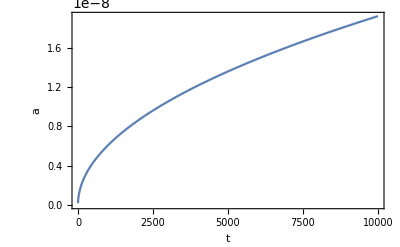

```mathematica
Plot[a1[t], {t, ti, 10000}, AxesLabel->{t,a},Frame->True, PlotRangePadding->0 ]
```

```mathematica
ar := ati/ti^(1/2)
aRad[t_]:= ar*t^(1/2)
```

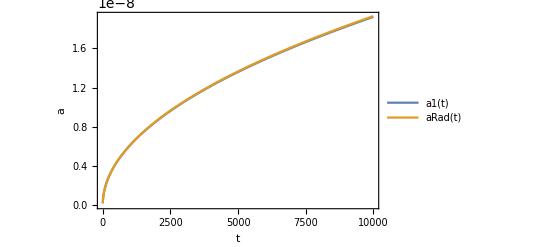

```mathematica
Plot[{a1[t], aRad[t]}, {t, ti, 10000}, PlotLegends->"Expressions", AxesLabel->{t,a}, Frame->True, PlotRangePadding->0]
```

```mathematica
ρbh[t_]:= ρbh0*(ati/a1[t])^2
```

```mathematica
ρbh[10^(-4)]
```

6.17199×10^-13

```mathematica
kvar[n_] = (4π *G)/(3*c^2)*ρbh0 *(ati)^(3-n)
ecuacion =a''[t]*a[t]+a'[t]^2-kvar[n]*a[t]^(n-1)==0
```

```mathematica
soln =ParametricNDSolveValue[{ecuacion, a[ti]==ati,a'[ti]==Dati}, a, {t, 10^(-4), ti}, {n}, PrecisionGoal->12,AccuracyGoal->12,MaxStepSize->0.001]
```

ParametricFunction[<>]

```mathematica
valorn := Range[-3, 3, 0.1]
```

```mathematica
lista  := Table[soln[n][t], {n, valorn}]
```

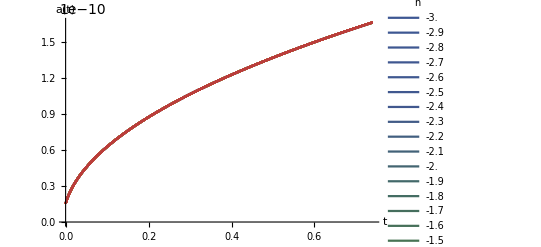

```mathematica
Plot[Evaluate[lista],{t,10^-4,ti},PlotLegends->LineLegend[valorn,LegendLabel->"n"],AxesLabel->{"t","a(t)"},PlotStyle->"DarkRainbow"]
```

```mathematica
ρbhvar[t_, n_]:= ρbh0*(ati/(soln[n][t]))^(3-n)
```

```mathematica
listaρbh  := Table[ρbhvar[t, n], {n, valorn}]
```

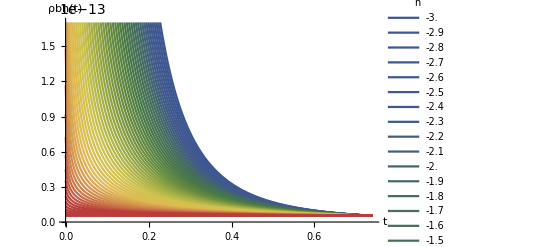

```mathematica
Plot[Evaluate[listaρbh],{t,10^-4,ti},PlotLegends->LineLegend[valorn,LegendLabel->"n"],AxesLabel->{"t","ρbh(t)"},PlotStyle->"DarkRainbow"]
```

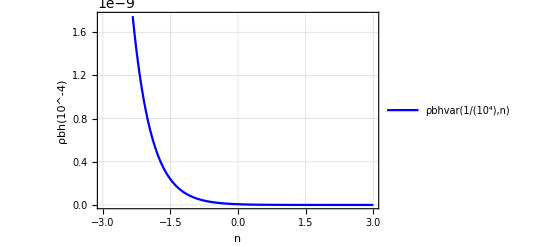

```mathematica
Plot[ρbhvar[10^-4,n],{n,-3,3},AxesLabel->{"n","ρbh(10^-4)"},PlotStyle->Directive[Thick,Blue],PlotTheme->"Detailed"]
```

```mathematica
ρbhvar[10^-4,1]
```

6.17489×10^-13